## b=1

```mathematica
data1=Drop[ToExpression/@Import[FileNameJoin[{"D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\b-LRWdata\\b-LRW-FromCluster\\b1LRW\\b=1.000000-LRW-3d-square-lattice-data-3-101.csv"}],"CSV"],2];
```

```mathematica
data2=Drop[ToExpression/@Import[FileNameJoin[{"D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\b-LRWdata\\b-LRW-FromCluster\\b1LRW\\b=1.000000-LRW-3d-square-lattice-data-103-201.csv"}],"CSV"],2];
```

```mathematica
data3=Drop[ToExpression/@Import[FileNameJoin[{"D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\b-LRWdata\\b-LRW-FromCluster\\b1LRW\\b=1.000000-LRW-3d-square-lattice-data-203-301.csv"}],"CSV"],2];
```

```mathematica
data4=Drop[ToExpression/@Import[FileNameJoin[{"D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\b-LRWdata\\b-LRW-FromCluster\\b1LRW\\b=1.000000-LRW-3d-square-lattice-data-303-401.csv"}],"CSV"],2];
```

```mathematica
data5=Drop[ToExpression/@Import[FileNameJoin[{"D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\b-LRWdata\\b-LRW-FromCluster\\b1LRW\\b=1.000000-LRW-3d-square-lattice-data-403-501.csv"}],"CSV"],2];
```

```mathematica
rawDatab1=joinedData=Join[data1,data2,data3,data4,data5];
```

## b=2

```mathematica
data1=Drop[ToExpression/@Import[FileNameJoin[{"D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\b-LRWdata\\b-LRW-FromCluster\\b2LRW\\b=2.000000-LRW-3d-square-lattice-data-3-201.csv"}],"CSV"],2];
```

```mathematica
data2=Drop[ToExpression/@Import[FileNameJoin[{"D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\b-LRWdata\\b-LRW-FromCluster\\b2LRW\\b=2.000000-LRW-3d-square-lattice-data-203-301.csv"}],"CSV"],2];
```

```mathematica
data3=Drop[ToExpression/@Import[FileNameJoin[{"D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\b-LRWdata\\b-LRW-FromCluster\\b2LRW\\b=2.000000-LRW-3d-square-lattice-data-303-401.csv"}],"CSV"],2];
```

```mathematica
rawDatab2=Join[data1,data2,data3];
```

## b=3

```mathematica
data1=Drop[ToExpression/@Import[FileNameJoin[{"D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\b-LRWdata\\b-LRW-FromCluster\\b3LRW\\b=3.000000-LRW-3d-square-lattice-data-3-201.csv"}],"CSV"],2];
```

```mathematica
data2=Drop[ToExpression/@Import[FileNameJoin[{"D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\b-LRWdata\\b-LRW-FromCluster\\b3LRW\\b=3.000000-LRW-3d-square-lattice-data-203-301.csv"}],"CSV"],2];
```

```mathematica
data3=Drop[ToExpression/@Import[FileNameJoin[{"D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\b-LRWdata\\b-LRW-FromCluster\\b3LRW\\b=3.000000-LRW-3d-square-lattice-data-303-401.csv"}],"CSV"],2];
```

```mathematica
data4=Drop[ToExpression/@Import[FileNameJoin[{"D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\b-LRWdata\\b-LRW-FromCluster\\b3LRW\\b=3.000000-LRW-3d-square-lattice-data-403-501.csv"}],"CSV"],2];
```

```mathematica
rawDatab3=joinedData=Sort[Join[data1,data2,data3,data4]];
```

## b=4

```mathematica
data1=DeleteCases[Drop[ToExpression/@Import[FileNameJoin[{"D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\b-LRWdata\\b-LRW-FromCluster\\b4LRW\\b=4.000000-LRW-3d-square-lattice-data-3-201.csv"}],"CSV"],2],{}];
```

```mathematica
data2=Drop[ToExpression/@Import[FileNameJoin[{"D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\b-LRWdata\\b-LRW-FromCluster\\b4LRW\\b=4.000000-LRW-3d-square-lattice-data-203-401.csv"}],"CSV"],2];
```

```mathematica
data3=Drop[ToExpression/@Import[FileNameJoin[{"D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\b-LRWdata\\b-LRW-FromCluster\\b4LRW\\b=4.000000-LRW-3d-square-lattice-data-403-501.csv"}],"CSV"],2];
```

```mathematica
(*data4=Drop[ToExpression/@Import[FileNameJoin[{"D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\b-LRWdata\\b-LRW-FromCluster\\b4LRW\\b=4.000000-LRW-3d-square-lattice-data-403-501.csv"}],"CSV"],2];*)
```

```mathematica
rawDatab4=joinedData=Join[data1,data2,data3(*,data4*)];
```

## b=5

```mathematica
data1=DeleteCases[Drop[ToExpression/@Import[FileNameJoin[{"D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\b-LRWdata\\b-LRW-FromCluster\\b5LRW\\b=5.000000-LRW-3d-square-lattice-data-3-201.csv"}],"CSV"],1],{}];
```

```mathematica
data2=Drop[ToExpression/@Import[FileNameJoin[{"D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\b-LRWdata\\b-LRW-FromCluster\\b5LRW\\b=5.000000-LRW-3d-square-lattice-data-203-301.csv"}],"CSV"],1];
```

```mathematica
data3=Drop[ToExpression/@Import[FileNameJoin[{"D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\b-LRWdata\\b-LRW-FromCluster\\b5LRW\\b=5.000000-LRW-3d-square-lattice-data-303-401.csv"}],"CSV"],1];
```

```mathematica
data4=Drop[ToExpression/@Import[FileNameJoin[{"D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\b-LRWdata\\b-LRW-FromCluster\\b5LRW\\b=5.000000-LRW-3d-square-lattice-data-403-501.csv"}],"CSV"],1];
```

```mathematica
(*data5=Drop[ToExpression/@Import[FileNameJoin[{"D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\b-LRWdata\\b-LRW-FromCluster\\b5LRW\\b=5.000000-LRW-3d-square-lattice-data-503-601.csv"}],"CSV"],2];*)
```

```mathematica
rawDatab5=joinedData=Join[data1,data2,data3,data4(*,data5*)];
```

# Plot

```mathematica
lm1=LinearModelFit[Log[rawDatab1],x,x]
lm2=LinearModelFit[Log[rawDatab2],x,x]
lm3=LinearModelFit[Log[rawDatab3],x,x]
lm4=LinearModelFit[Log[rawDatab4],x,x]
lm5=LinearModelFit[Log[rawDatab5],x,x]
```

FittedModel[…]

FittedModel[…]

FittedModel[…]

«2 more identical outputs»

```mathematica
lm1["ParameterErrors"][[2]]
lm2["ParameterErrors"][[2]]
lm3["ParameterErrors"][[2]]
lm4["ParameterErrors"][[2]]
lm5["ParameterErrors"][[2]]
```

0.0306181

0.0399351

0.0237014

0.0144462

0.0145876

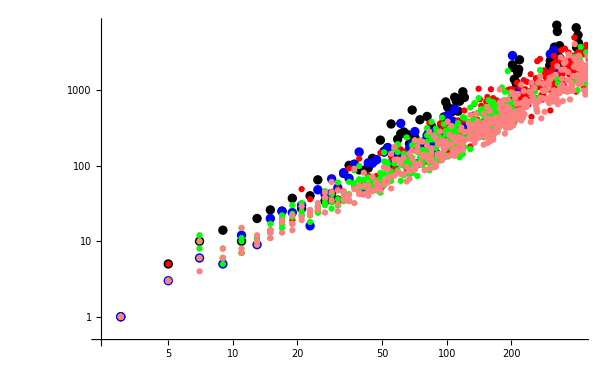

```mathematica
Show[{ListLogLogPlot[rawDatab1,PlotStyle->{Black}],
ListLogLogPlot[rawDatab2,PlotStyle->{Blue}],
ListLogLogPlot[rawDatab3,PlotStyle->{Red}],
ListLogLogPlot[rawDatab4,PlotStyle->{Green}],
ListLogLogPlot[rawDatab5,PlotStyle->{Pink}]}]
```